## Rules

A rule is an ordered pair that creates a mapping from one Mathematica expression, to another. We’ve seen it before:

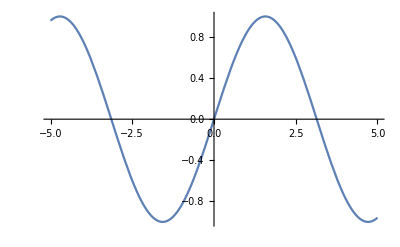

```mathematica
Plot[Sin[x],{x,-5,5},ImageSize->Tiny]
```

Here, ImageSize -> Tiny is a rule. Typically, options in Mathematica are represented as rules:

```mathematica
?Rule
```

lhs->rhs or lhs→rhs represents a rule that transforms lhs to rhs.

Suppose you have an expression:

```mathematica
list={1,2,3,1,2,3}
```

{1,2,3,1,2,3}

And you want to change every instance of 1 to x. The easiest way to do this is with a rule transformation and the ReplaceAll function:

```mathematica
?ReplaceAll
```

expr/.rules applies a rule or list of rules in an attempt to transform each subpart of an expression expr. 
ReplaceAll[rules] represents an operator form of ReplaceAll that can be applied to an expression.

```mathematica
ReplaceAll[list,1->x]
```

{x,2,3,x,2,3}

Notice that the rule by itself is not enough to transform the expression. We need the ReplaceAll function to actually apply the transformation defined by the rule. Let’s use the shorthand for ReplaceAll:

```mathematica
list/. 1->x
```

{x,2,3,x,2,3}

Let’s say we further wanted to transform 2 to y, we would simply put the rules in a list:

```mathematica
list/.{1->x,2->y}
```

{35,81,x,y,3,15,20}

A rule can transform any expression to any other expression. For example:

```mathematica
list/.{1->x,2->y,3->Plot[Sin[x],{x,-5,5},ImageSize->Tiny]}
```

{x,y,-Graphics-,x,y,-Graphics-}

This construct enables us to transform any Mathematica expression, which is a very powerful thing, as you will discover the more you work with Mathematica. For example, the argument of an expression:

```mathematica
Sin[x]/.x->3
```

Sin[3]

Replace the Head of an expression:

```mathematica
Sin[x]/.Sin->Cos
```

Cos[x]

You can even match entire expressions, like the Sin[x]:

```mathematica
Sin[x]+y/.Sin[x]->y^2
```

y+y^2

Note: If there are two rules with the same key values, the first one takes precedence.

```mathematica
list/.{3->"cat",3->"Dog"}
```

{1,2,cat,1,2,cat}

### ReplaceRepeated

In the following expression we replace {4} -> 4.

```mathematica
{1,{{{4}}},5}/.{4}->4
```

{1,{{4}},5}

Notice that it reduced the depth by 1. If we wanted to keep applying this rule until 4 is no longer nested, we can use ReplaceRepeated

```mathematica
?ReplaceRepeated
```

expr//.rules repeatedly performs replacements until expr no longer changes.

```mathematica
ReplaceRepeated[{1,{{{4}}},5},{4}->4]
```

{1,4,5}

The shorthand for replace repeated is //.

```mathematica
{1,{{{4}}},5}//.{4}->4
```

{1,4,5}

```mathematica
nestedList={1,{{{4}}},5}
```

{1,{{{4}}},5}

```mathematica
nestedList=nestedList/.{4}->4
```

{1,4,5}

You need to be careful with this. Using this function, you can easily send your program into infinite loops. For example:

```mathematica
f[x]/.x->f[x]
```

f[f[x]]

Will give you a nested expression. If we used ReplaceRepeated, the replacement rule will take place an infinite number of times.

As you can imagine, rules are a very powerful language feature. If rules are bread, patterns are butter.

## Patterns

Patterns enable Mathematica to represent classes of expressions.

For example, suppose we wanted to replace all the integers in a list. We need something that represents the class of Integers. We can test if something belongs to a class using MatchQ:

```mathematica
?MatchQ
```

MatchQ[expr,form] returns True if the pattern form matches expr, and returns False otherwise.
MatchQ[form] represents an operator form of MatchQ that can be applied to an expression.

The class of something is the head of the expression. For the class of integers, we would write:

```mathematica
MatchQ[1,_Integer]
```

True

```mathematica
MatchQ[.1,_Integer]
```

False

The underscore (_) is known as Blank.

```mathematica
?Blank
```

_ or Blank[] is a pattern object that can stand for any Wolfram Language expression. 
_h or Blank[h] can stand for any expression with head h.

The word appearing after the Blank is the Head of the expression that we are interested in. Let’s create a list:

```mathematica
list={1.1,2,x,3.14,{π,2}}
```

{1.1,2,x,3.14,{π,2}}

To replace all integers in the list:

```mathematica
list/.{_Integer->"This was an integer"}
```

{1.1,This was an integer,x,3.14,{π,This was an integer}}

If we look at the Head of 2, it is an Integer:

```mathematica
Head[2]
```

Integer

Whereas the Head of 1.1 is not Integer:

```mathematica
Head[1.1]
```

Real

Notice that the rule replacement worked at multiple depths. ReplaceAll recurses into an expression until it matches, and then performs the replacement. If we left out the Head in the pattern, then the pattern would only match the top most expression.

```mathematica
list/.{x_->F[x]}
```

F[{1.1,2,x,3.14,{π,2}}]

So the rule replacement was not applied to it. We can even name the patterns to work with the matched expression:

```mathematica
list/.{x_Integer->Sin[x]}
```

{1.1,Sin[2],x,3.14,{π,Sin[2]}}

Note that x_Integer is called a named pattern. Mathematica’s FullForm of the expression looks like this:

```mathematica
FullForm[x_Integer]
```

Pattern[x,Blank[Integer]]

The Head is Pattern:

```mathematica
?Pattern
```

RowBox[{StyleBox["s", "TI"], ":", StyleBox["obj", "TI"]}] represents the pattern object StyleBox["obj", "TI"], assigned the name StyleBox["s", "TI"].

The shorthand for pattern is ‘:’. We could write this as:

```mathematica
x:Blank[Integer]
```

x_Integer

```mathematica
list/.{x:_Integer->Sin[x]}
```

{Sin[35],Sin[81],Sin[1],Sin[2],Sin[3],Sin[15],Sin[20]}

### Multiple objects

Let’s look at an interesting problem. Suppose you had a random list and you wanted to identify occurrences of 1, 2 and 3, and replace them with “Eureka”.

Let’s generate our random list:

```mathematica
?RandomInteger
```

RandomInteger[{i_min,i_max}] gives a pseudorandom integer in the range {i_min,i_max}. 
RandomInteger[i_max] gives a pseudorandom integer in the range {0,…,i_max}. 
RandomInteger[] pseudorandomly gives 0 or 1. 
RandomInteger[range,n] gives a list of n pseudorandom integers. 
RandomInteger[range,{n_1,n_2,…}] gives an n_1×n_2×… array of pseudorandom integers.

```mathematica
list=Join[RandomInteger[100,2],{1,2,3},RandomInteger[100,2]]
```

{35,81,1,2,3,15,20}

If we knew ahead of time that we will have two elements before and after our sequence, then we can do something like:

```mathematica
list/.{a_,b_,1,2,3,c_,d_}->{a,b,"Eureka",c,d}
```

{35,81,Eureka,15,20}

That worked, but good programmers are generalists. Our pattern will only match expressions that begin and end with two elements. To represent sequences of expressions, we need BlankSequence (__):

```mathematica
?BlankSequence
```

__ (two _ characters) or BlankSequence[] is a pattern object that can stand for any sequence of one or more Wolfram Language expressions. 
__h or BlankSequence[h] can stand for any sequence of one or more expressions, all of which have head h.

Now we can do:

```mathematica
list/.{a__,1,2,3,b__}->{a,"Eureka",b}
```

{35,81,Eureka,15,20}

That worked well, but what if the sequence of 1, 2, 3 appeared in the beginning or the end of the list?

```mathematica
RotateLeft[list,2]/.{a__,1,2,3,b__}->{a,"Eureka",b}
```

{1,2,3,15,20,35,81}

Nothing happened! Because BlankSequences match one or more elements. If we want to match a pattern of zero or more elements, we use BlankNullSequence aka triple underscore (___):

```mathematica
RotateLeft[list,2]/.{a___,1,2,3,b___}->{a,"Eureka",b}
```

{Eureka,15,20,35,81}

This is truly powerful. Take a deep breath! You made it. In the next lecture we’ll look at PatternTests and Conditions.